#### Given a set L of closed intervals, calculate the minimal intervals with respect to the inclusion. That is, the output must be the subset of the intervals of L that do not include another of L.

```mathematica
MinimalIntervals[list_]:=Module[{ord=Ordering[list],listord=SortBy[list,ord]},
DeleteDuplicates[listord,IntervalIntersection[#1,#2]===#1&]
]
```

```mathematica
MinimalIntervals@{Interval[{6,7}],Interval[{6,8}],Interval[{1,2}],Interval[{1,3}]}
```

{Interval[{1,2}],Interval[{6,7}]}

```mathematica
intervalos={Interval[{6,7}],Interval[{6,8}],Interval[{1,2}],Interval[{1,3}],Interval[{2,3}],Interval[{1,10}],Interval[{7,9}],Interval[{1,8}],Interval[{3,4}]};
```

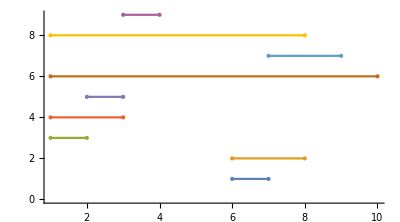

```mathematica
NumberLinePlot[intervalos]
```

```mathematica
MinimalIntervals@intervalos
```

{Interval[{1,2}],Interval[{2,3}],Interval[{3,4}],Interval[{6,7}],Interval[{7,9}]}

Función que nos da un único intervalo minimal o el conjunto vacío

```mathematica
MinimalIntervals2[list_]:=IntervalIntersection[Interval[Min/@Transpose[list[[All,1]]]],Interval[Max/@Transpose[list[[All,1]]]]]
```

```mathematica
MinimalIntervals2@{Interval[{6,7}],Interval[{6,8}],Interval[{1,7}]}
```

Interval[{6,7}]

```mathematica
MinimalIntervals2@{Interval[{6,7}],Interval[{6,8}],Interval[{1,2}]}
```

Interval[]